```mathematica
shape = 0.85
scale = 8.0
```

0.85

8.

```mathematica
0
```

0.5

8.

```mathematica
m[plc_]:= 1.0-Exp[-Power[plc/shape,scale]];
```

```mathematica
Plot[m[plc/100],{plc, 0,100}, Frame->True, FrameLabel->{"Percentage loss of conductivity", "Mortality probability"}, LabelStyle->16, PlotRange->All]
```

-Graphics-

```mathematica
path= "/Users/pp/Dropbox/UNI/Projekte/A03_Hydraulics_Implementation/Analysis/AllCavCurves05-2020.tsv";
```

```mathematica
psi50s = Import[path][[All,1]];
```

```mathematica
slopes = Import[path][[All,2]];
```

```mathematica
cav [psi_,psi50_ , slope_]:= 1/(1+(psi/psi50)^slope)
```

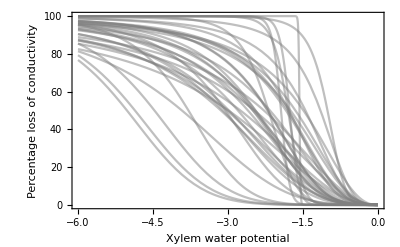

```mathematica
s =  Plot[Table[100cav[psi,psi50s[[i]],slopes[[i]]],{i,1,37}], {psi, -6,0}, Frame->True,PlotStyle->{Directive[Gray, Opacity[0.5]]}, LabelStyle->16,FrameLabel->{"Xylem water potential", "Percentage loss of conductivity"}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pp/Dropbox/UNI/Projekte/A03_Hydraulics_Implementation

```mathematica
Export["PLC-Xylem.png", s, "ImageResolution"->300]
```

PLC-Xylem.png

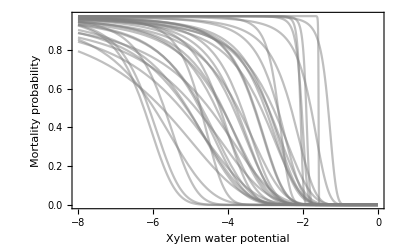

```mathematica
Plot[Table[m[cav[psi,psi50s[[i]],slopes[[i]]]],{i,1,37}], {psi, -8,0}, Frame->True, PlotStyle->{Directive[Gray, Opacity[0.5]]},FrameLabel->{"Xylem water potential", "Mortality probability"}, LabelStyle->16]
```

```mathematica
1200000/39408.0
```

30.4507

```mathematica
39408.0/12
```

3284.

```mathematica
%/5
```

656.8

```mathematica
1-(1-0.1)^2
```

0.19

```mathematica
365*48
```

17520

```mathematica
0.8 *1.1
```

0.88

```mathematica
0.8*0.9
```

0.72

```mathematica
{0.9, 0.95, 1.0, 1.05, 1.1}   * 0.8
```

{0.72,0.76,0.8,0.84,0.88}

```mathematica
{0.9, 0.95, 1.0, 1.05, 1.1}   * 8
```

{7.2,7.6,8.,8.4,8.8}

```mathematica
0.5*1000/96.
```

5.20833